# ALL PRACTICALS

# practicals 1 date: 01/19/23

1  1.  0.25

2  0.25  0.186441

3  0.186441  0.201736

4  0.201736  0.20164

5  0.20164  0.20164

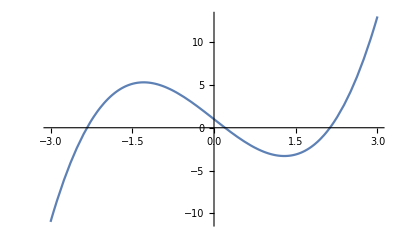

1  1.  0.25

2  0.25  0.186441

3  0.186441  0.201736

4  0.201736  0.20164

5  0.20164  0.20164

root = 0.20164

```mathematica
regulaFalsi[f_, xo_, xo1_, n_] := Module[{}, prev=N[xo];next=N[xo1];
If[f[prev]*f[next] > 0, Print["regula falsi can not be applied "]; Return[]];
i=1;
While[i ≤n,
temp = next;
next = (prev*f[next]-next*f[prev])/(f[next]-f[prev]);
prev = temp;
Print[i, "  ", prev, "  ", next];
i++;];
Print["root = ", next]]
f[x_]=x^3-5x+1;
Plot[f[x], {x, -3, 3}]
regulaFalsi[f, 0,1, 5]
```

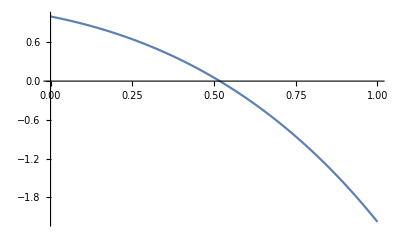

1  1.  0.314665

2  0.314665  0.446728

3  0.446728  0.531706

4  0.531706  0.516904

5  0.516904  0.517747

root = 0.517747

```mathematica
f[x_] = Cos[x]-x*Exp[x];
Plot[f[x], {x, 0,1}]
regulaFalsi[f,0,1,5]
```

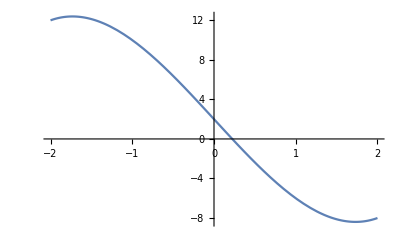

```mathematica
f[x_] = x^3-9*x +2;
Plot[f[x], {x, -2,2}]
```

```mathematica
regulaFalsi[f, 0, 1, 5]
```

1  1.  0.25

2  0.25  0.219512

3  0.219512  0.22347

4  0.22347  0.223462

5  0.223462  0.223462

root = 0.223462

# practicals 1 19/01/23

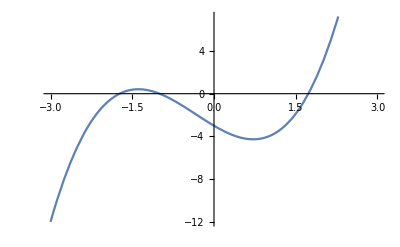

1    1.5    2.   -1.875

2    1.5    1.75   -1.875

3    1.625    1.75   -0.943359

4    1.6875    1.75   -0.409424

5    1.71875    1.75   -0.124786

Root = 1.73438

```mathematica
bisection[f_, a0_, b0_, n_]:= Module[{}, a = N[a0];b = N[b0];If[f[a]*f[b] > 0, Print["bisection method can not be applied"];
Return[]];
p = (a+b)/2;
i=1;
While[i ≤ n, 
If[f[a]*f[p]<0, b=p,a=p];
Print[i, "    ", a, "    ", b, "   ",f[a]];
i++;
p = (a+b)/2];
Print["  Root = ", p]]
f[x_]:= x^3+x^2-3*x-3;
Plot[f[x],{x,-3,3}]
bisection[f,1,2,5]
```

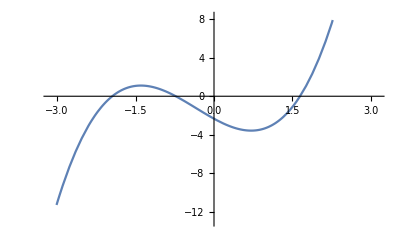

1    1.5    2.   -1.875

2    1.5    1.75   -1.875

3    1.625    1.75   -0.943359

4    1.6875    1.75   -0.409424

5    1.71875    1.75   -0.124786

Root = 1.73438

```mathematica
f[x_]  = x^3-5x+1;
Plot[f[x], {x, -3, 3}]
bisection[f, 0,1,5]
```

-Graphics-

1    0.    0.5

2    0.    0.25

3    0.125    0.25

4    0.1875    0.25

5    0.1875    0.21875

Root = 0.203125

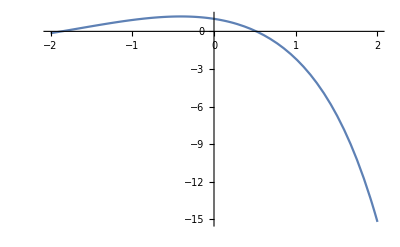

1    0.5    1.

2    0.5    0.75

3    0.5    0.625

4    0.5    0.5625

5    0.5    0.53125

Root = 0.515625

```mathematica
f[x_]=Cos[x]-x*Exp[x];
Plot[f[x], {x, -2,2}]
bisection[f,0,1,5]
```

# Practicals 1 date: 01/19/23

```mathematica
secantMethod[f_, xo_, xo1_, n_] := Module[{}, 
prev=N[xo];
next=N[xo1];
i=1;
While[i ≤n,
temp = next;
next = (prev*f[next]-next*f[prev])/(f[next]-f[prev]);
prev = temp;
Print[i, "  ", prev, "  ", next];
i++;];
Print["root = ", next]]
f[x_]=x^3-5x+1;
Plot[f[x], {x, -3, 3}]
secantMethod[f, 0, 1,5]
```

-Graphics-

1  1.  0.25

2  0.25  0.186441

3  0.186441  0.201736

4  0.201736  0.20164

5  0.20164  0.20164

root = 0.20164

```mathematica
f[x_] = Cos[x] - x*Exp[x];
Plot[f[x], {x, -2, 2}]
```

-Graphics-

```mathematica
regulaFalsi[f, 0, 1, 5]
```

1  1.  0.314665

2  0.314665  0.446728

3  0.446728  0.531706

4  0.531706  0.516904

5  0.516904  0.517747

root = 0.517747

```mathematica
f[x_] = x^3-9*x +2;
Plot[f[x], {x, -2,2}]
```

-Graphics-

```mathematica
regulaFalsi[f, 0, 1, 5]
```

1  1.  0.25

2  0.25  0.219512

3  0.219512  0.22347

4  0.22347  0.223462

5  0.223462  0.223462

root = 0.223462

# Practicals 3 date: 09/02/23

```mathematica
newtonRaphson[f_, p0_, n_] :=Module[{},pold=N[p0];
i=1;
df[x_]=D[f[x],x];
While[i≤n,
pnew=N[pold-N[f[pold]]/N[df[pold]]];
Print[i, "    ", pnew];
i++;
pold=pnew];
Print[" Root = " , pnew]]

f[x_] = Cos[x]-x*Exp[x];
Plot[f[x], {x, -2, 2}]
```

-Graphics-

```mathematica
newtonRaphson[f, 0, 5]
```

1    1.

2    0.653079

3    0.531343

4    0.51791

5    0.517757

Root = 0.517757

```mathematica
f[x_] = x^3-5x+1;
Plot[f[x], {x,-3, 3}]
```

-Graphics-

```mathematica
newtonRaphson[f, 0, 5]
```

1    0.2

2    0.201639

3    0.20164

4    0.20164

5    0.20164

Root = 0.20164

```mathematica
f[x_] = x^3-9*x +2;
Plot[f[x], {x, -2,2}]
newtonRaphson[f, 0, 5]
```

-Graphics-

1    0.222222

2    0.223462

3    0.223462

4    0.223462

5    0.223462

Root = 0.223462

# Practicals 4 date: 16/03/2023 Gauss elimination method

```mathematica
gausselimination[mat_] := Module[{m=mat,  n = Length[mat]},
Print["initial matrix is:\n", MatrixForm[m]];
For[i=1,i≤n-1,i++,
For[j=i+1, j≤n, j++,
m[[j]]=m[[j]]-m[[i]]/m[[i,i]]*m[[j,i]];
]
];
Print["after making lower trianglular:\n", MatrixForm[m]];
For[i=n,i≥1,i--,

]
]
m1 = Table[10i+j, {i, 3}, {j,4}];
gausselimination[m1];
m2 = {{2,3,1,1},{1,2,2,4},{1,3,1,3}};
gausselimination[m2];
```

initial matrix is:
(11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34)

after making lower trianglular:
(11 | 12 | 13 | 14
0 | -10/11 | -20/11 | -30/11
0 | 0 | 0 | 0)

initial matrix is:
(2 | 3 | 1 | 1
1 | 2 | 2 | 4
1 | 3 | 1 | 3)

after making lower trianglular:
(2 | 3 | 1 | 1
0 | 1/2 | 3/2 | 7/2
0 | 0 | -4 | -8)

# Practicals 4 date: 16/03/2023 Gauss elimination method using inbuilt function

```mathematica
gausselimination[mat_, last_] := Module[{a=mat,  n = Length[mat], b =last },
aug=ArrayFlatten[{{a,b}}];
Print["augmented matrix is:\n", MatrixForm[aug]];
Print[MatrixForm[RowReduce[aug]]];
Print[LinearSolve[a,b]];
]
m = {{2,3,1},{1,2,2},{1,3,1}};
l = {{1},{4},{3}};
gausselimination[m,l];
```

augmented matrix is:
(2 | 3 | 1 | 1
1 | 2 | 2 | 4
1 | 3 | 1 | 3)

(1 | 0 | 0 | -2
0 | 1 | 0 | 1
0 | 0 | 1 | 2)

{{-2},{1},{2}}

```mathematica
|
```

# Practicals 5 Gauss Jacobi method date: 06/04/2023

```mathematica
GaussJacobi[a0_, b0_, x0_, max_] :=
Module[{a=N[a0], b=N[b0], i, j, k=0, n=Length[x0], x=x0, xold=x0},
Print["x0=", x];
While[k<max,
For[i=1, i≤ n, i = i+1,
x[[i]]=(b[[i]]+a[[i,i]]*xold[[i]]- ∑_(j=1)^n a[[i,j]]*xold[[j]])/a[[i,i]]];
Print["x", k+1, "=", x];
xold=x;
k=k+1;];
]
```

```mathematica
a0=({{4, -1, 0}, {-1, 4, -1}, {0, -1, 4}})
b0=({{2}, {4}, {10}})
x0=({{0}, {0}, {0}})
GaussJacobi[a0, b0, x0, 10];
```

{{4,-1,0},{-1,4,-1},{0,-1,4}}

{{2},{4},{10}}

{{0},{0},{0}}

x0={{0},{0},{0}}

x1={{0.5},{1.},{2.5}}

x2={{0.75},{1.75},{2.75}}

x3={{0.9375},{1.875},{2.9375}}

x4={{0.96875},{1.96875},{2.96875}}

x5={{0.992188},{1.98438},{2.99219}}

x6={{0.996094},{1.99609},{2.99609}}

x7={{0.999023},{1.99805},{2.99902}}

x8={{0.999512},{1.99951},{2.99951}}

x9={{0.999878},{1.99976},{2.99988}}

x10={{0.999939},{1.99994},{2.99994}}

```mathematica
a0=({{4, 1, 1}, {1, 5, 2}, {1, 2, 3}})
b0=({{2}, {-6}, {-4}})
x0=({{0}, {0}, {0}})
GaussJacobi[a0, b0, x0, 10];
```

{{4,1,1},{1,5,2},{1,2,3}}

{{2},{-6},{-4}}

{{0},{0},{0}}

x0={{0},{0},{0}}

x1={{0.5},{-1.2},{-1.33333}}

x2={{1.13333},{-0.766667},{-0.7}}

x3={{0.866667},{-1.14667},{-1.2}}

x4={{1.08667},{-0.893333},{-0.857778}}

x5={{0.937778},{-1.07422},{-1.1}}

x6={{1.04356},{-0.947556},{-0.929778}}

x7={{0.969333},{-1.0368},{-1.04948}}

x8={{1.02157},{-0.974074},{-0.965244}}

x9={{0.98483},{-1.01822},{-1.02447}}

x10={{1.01067},{-0.987176},{-0.982799}}

```mathematica
Practicals 6
Gauss Seidel method
date: 06/04/2023
```

```mathematica
GaussSeidel[a0_, b0_, x0_, max_] :=
Module[{a=N[a0], b=N[b0], i, j, k=0, n=Length[x0], x=x0},
Print["x0=", x];
While[k<max,
For[i=1, i≤ n, i = i+1,
x[[i]]=(b[[i]]+a[[i,i]]*x[[i]]- ∑_(j=1)^n a[[i,j]]*x[[j]])/a[[i,i]]];
Print["x", k+1, "=", x];
k=k+1;];
]
```

```mathematica
a0=({{8, 1, -1}, {-1, 7, -2}, {2, 1, 9}})
b0=({{8}, {4}, {12}})
x0=({{0}, {0}, {0}})
GaussSeidel[a0, b0, x0, 10];
```

{{8,1,-1},{-1,7,-2},{2,1,9}}

{{8},{4},{12}}

{{0},{0},{0}}

x0={{0},{0},{0}}

x1={{1.},{0.714286},{1.03175}}

x2={{1.03968},{1.01474},{0.989544}}

x3={{0.996851},{0.996563},{1.00108}}

x4={{1.00056},{1.00039},{0.999831}}

x5={{0.99993},{0.999942},{1.00002}}

x6={{1.00001},{1.00001},{0.999997}}

x7={{0.999999},{0.999999},{1.}}

x8={{1.},{1.},{1.}}

x9={{1.},{1.},{1.}}

x10={{1.},{1.},{1.}}

```mathematica
a0=({{45, 2, 3}, {-3, 22, 2}, {5, 1, 20}})
b0=({{58}, {47}, {67}})
x0=({{0}, {0}, {0}})
GaussJacobi[a0, b0, x0, 10];
```

{{45,2,3},{-3,22,2},{5,1,20}}

{{58},{47},{67}}

{{0},{0},{0}}

x0={{0},{0},{0}}

x1={{1.28889},{2.13636},{3.35}}

x2={{0.970606},{2.00758},{2.92096}}

x3={{1.00493},{2.00318},{3.00697}}

x4={{0.999394},{2.00004},{2.99861}}

x5={{1.00009},{2.00004},{3.00015}}

x6={{0.999988},{2.},{2.99998}}

x7={{1.},{2.},{3.}}

x8={{1.},{2.},{3.}}

x9={{1.},{2.},{3.}}

x10={{1.},{2.},{3.}}

```mathematica
a0=({{4, -1, 0}, {-1, 4, -1}, {0, -1, 4}})
b0=({{2}, {4}, {10}})
x0=({{0}, {0}, {0}})
GaussSeidel[a0, b0, x0, 10]
```

{{4,-1,0},{-1,4,-1},{0,-1,4}}

{{2},{4},{10}}

{{0},{0},{0}}

x0={{0},{0},{0}}

x1={{0.5},{1.125},{2.78125}}

x2={{0.78125},{1.89063},{2.97266}}

x3={{0.972656},{1.98633},{2.99658}}

x4={{0.996582},{1.99829},{2.99957}}

x5={{0.999573},{1.99979},{2.99995}}

x6={{0.999947},{1.99997},{2.99999}}

x7={{0.999993},{2.},{3.}}

x8={{0.999999},{2.},{3.}}

x9={{1.},{2.},{3.}}

x10={{1.},{2.},{3.}}

# Practicals 7 divided difference date 13/04/2023

```mathematica
sum =0;
points = {{3, 293},{5, 508},{6, 585},{9,764}};
n = Length[points]
y = points[[All, 1]]
f = points[[All, 2]]
dd[k_]:=Sum[(f[[i]]/Product[If[Equal[j, i],1,(y[[i]]-y[[j]])], {j, 1,k}]), {i, 1, k}]
p[x_]=Sum[(dd[i]*Product[If[i≤j, 1, x-y[[j]]], {j, 1, i-1}]), {i, 1, n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

4

{3,5,6,9}

{293,508,585,764}

293+215/2 (-3+x)-61/6 (-5+x) (-3+x)+35/36 (-6+x) (-5+x) (-3+x)

1/36 (-9702+9003 x-856 x^2+35 x^3)

222.288

# Practicals 7 Simpson’s 1/3 rule date : 13/04/2023

```mathematica
a=Input["enter the left end point : "];
b =Input["enter the right end point : "];
n = Input["enter the number of sub intrevals tyo be formed : "];
h=(b-a)/n;
y=Table[a+ih, {i, 1, n}];
f[x]:=1/x;
sumodd=0;
sumeven=0;
For[i=1, i< n, i+=2, sumodd+=4*f[x]/.x->y[[i]]];
For[i=2, i<n, i+=2, sumeven+=2*f[x]/.x->y[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["for n = ", n, ", simpson estimate is : ", Sn]
in = Integrate[1/x, {x,1,2}]
Print["true value is ", in]
Print["absolute error is ", Abs[Sn-in]]
```

for n = 2, simpson estimate is : 1/6 (1.5+4./(1.+ih))

Log[2]

true value is Log[2]

absolute error is Abs[1/6 (1.5+4./(1.+ih))-Log[2]]

# Practicals 7 Trapezoidal rule date: 13/04/2023

```mathematica
ClearAll[n,x,f, h, a, b, sum]
a = Input["enter the left end point : "]
b = Input["enter the right end point : "]
n = Input["enter the number of sub intervals to be formed : "]
sum = 0;
h  = (b-a)/n
f[x] = Sin[x]
For[i=1, i≤n-1, i++, sum += N[f[x]/.x->(a+i*h)]]
sum = N[(2*sum+f[x]/.x->a+f[x]/.x->b)*h/2]
```

0

2 π

50

π/25

Sin[x]

-1.74393×10^-16

# Practicals 7 Euler’s method date : 13/04/2023

```mathematica
Euler[a0_,b0_,h0_,f_,alpha_]:=Module[{a=N[a0],b=N[b0],h=N[h0],n,x},
n=(b-a)/h;
y[0]=alpha;
For[i=0,i≤n,i++,
x[i]=a+h*i;
y[i+1]=y[i]+h*f[x[i],y[i]];
Print["value at x[",i,"]=" x[i]," is ",y[i]];
];
];
f[x_,y_]:=y*x^3-1.5*y;
Euler[0,2,0.5,f,1]
```

value at x[00. is 1

value at x[10.5 ]= is 0.25

value at x[21. ]= is 0.078125

value at x[31.5 ]= is 0.0585938

value at x[42. ]= is 0.113525

# Practicals 7 Lagrange Interpolating polynomial date: 13/04/2023

```mathematica
ClearAll; 
points = {{1,0},{3,18},{4, 48},{6, 180},{10, 900}};
N0 = Length[points];
y = points[[All, 1]];
f= points[[All, 2]];
lagrange[sizee_, n_]:= Product[If[Equal[k,n],1,(x-y[[k]])/(y[[n]]-y[[k]])],{k,1,sizee}]  ;
Approx = Expand[Simplify[Sum[(f[[i]]*lagrange[N0, i]), {i,1,N0}]]]
```

-x^2+x^3

```mathematica
Approx/.x->5
```

100

```mathematica
Print[points]
```

{{1,0},{3,18},{4,48},{6,180},{10,900}}